# h=A+B+A^-1+B^-1

Extrapolation of  the ||M_n|| norms described in the paper
“A COMPUTATIONAL APPROACH TO THE THOMPSON GROUP F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
norms={{1,4.},{2,7.000000000000001},{3,8.605551275463988},{4,9.541381265149111},{5,10.187816020025469},{6,10.656244451028344},{7,11.022388732772455},{8,11.308130917701545},{9,11.545716716541902},{10,11.743086500427827},{11,11.913803073100125},{12,12.05981096300795},{13,12.189380782293503},{14,12.302920985302379},{15,12.405655196592425},{16,12.49714624116274},{17,12.580970148269211},{18,12.656602089719547},{19,12.726679068950057},{20,12.790534930918907},{21,12.850169509154144},{22,12.904982146260096},{23,12.956513938208243},{24,13.004187392723907}};
{xx,yy}=Transpose[norms];
norms=Transpose[{xx,yy^(1/2)}];
norms//MatrixForm
Ntuple=Length[norms]
```

(1 | 2.
2 | 2.64575
3 | 2.93352
4 | 3.08891
5 | 3.19184
6 | 3.26439
7 | 3.32
8 | 3.36276
9 | 3.3979
10 | 3.42682
11 | 3.45164
12 | 3.47272
13 | 3.49133
14 | 3.50755
15 | 3.52217
16 | 3.53513
17 | 3.54697
18 | 3.55761
19 | 3.56745
20 | 3.57639
21 | 3.58471
22 | 3.59235
23 | 3.59952
24 | 3.60613)

24

```mathematica
variance=Function[d,Module[{nlm,a,b,c,f,g,h},
nlm=NonlinearModelFit[norms⟦Range[8,24]⟧,a-b ((x-d )^(-c)),{a,b,c},x];
{f,g,h}=nlm[{"BestFit","FitResiduals","ParameterTable"}];
Total[g^2]/(Length[g]-1)(*variance*)
]]
upperlimit=Function[d,Module[{nlm,aa,a,b,c,f,g,h},
nlm=NonlinearModelFit[norms⟦Range[8,24]⟧,a-b ((x-d )^(-c)),{a,b,c},x];
aa=nlm["BestFitParameters"];
a/.aa
]]
```

Function[d,Module[{nlm,a,b,c,f,g,h},nlm=NonlinearModelFit[norms⟦Range[8,24]⟧,a-b (x-d)^-c,{a,b,c},x];{f,g,h}=nlm[{BestFit,FitResiduals,ParameterTable}];Total[g^2]/(Length[g]-1)]]

Function[d,Module[{nlm,aa,a,b,c,f,g,h},nlm=NonlinearModelFit[norms⟦Range[8,24]⟧,a-b (x-d)^-c,{a,b,c},x];aa=nlm[BestFitParameters];a/.aa]]

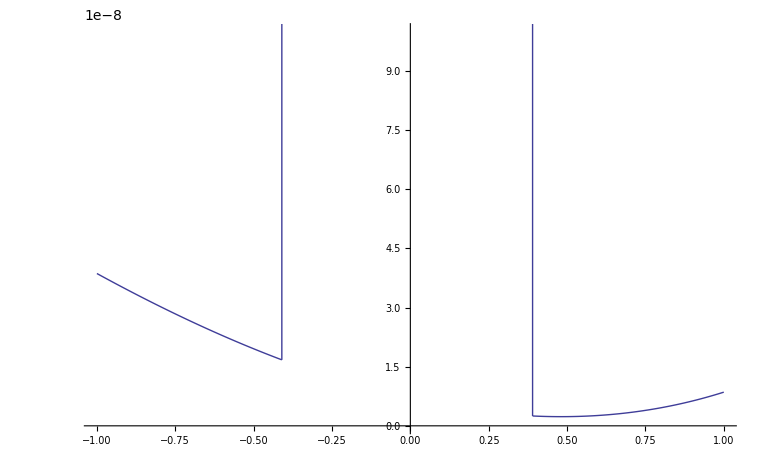

```mathematica
(*Graph d vs. variance(d)*)
varValues=Table[{d,variance[d]},{d,-1,1,.005}];
ListPlot[varValues,Joined->True,PlotRange->{0,10^-7}]
```

{-0.41,1.67381×10^-8}

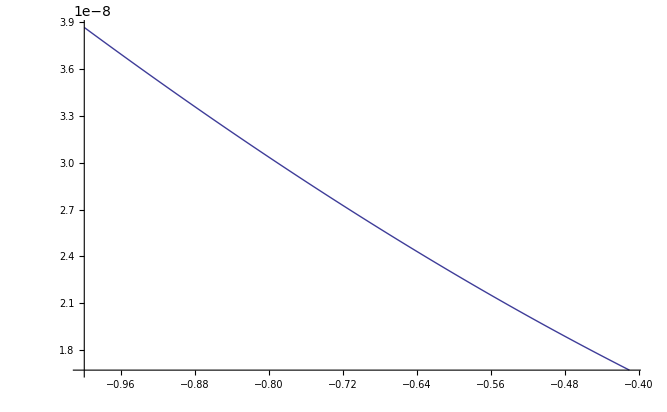

```mathematica
(*Graph d vs. variance(d)*)
varValues=Table[{d,variance[d]},{d,-1,-.40005,.01}];
varValues⟦-1⟧
ListPlot[varValues,Joined->True]
```

{1.,8.5409×10^-9}

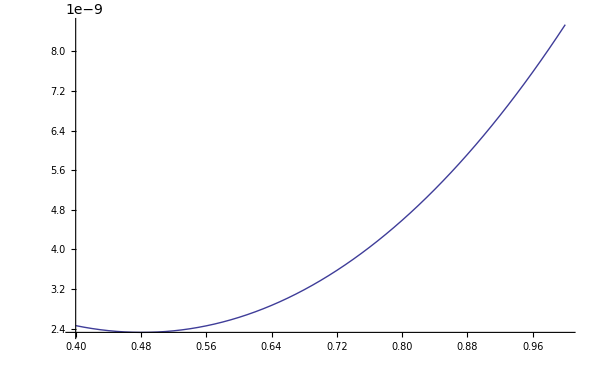

```mathematica
(*Graph d vs. variance(d)*)
varValues=Table[{d,variance[d]},{d,.4,1,.01}];
varValues⟦-1⟧
ListPlot[varValues,Joined->True]
```

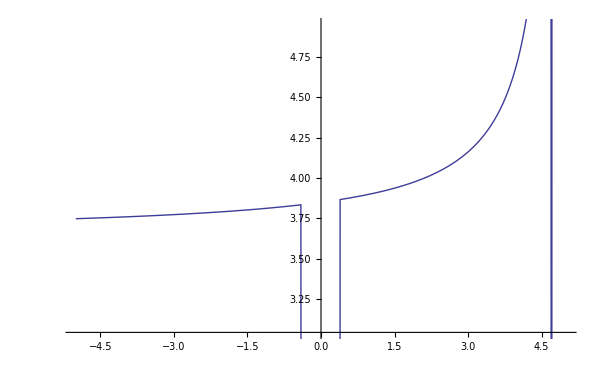

```mathematica
(*Graph d vs. a=upperbound*)
upperlimitValues=Table[{d,upperlimit[d]},{d,-5,5,.01}];
ListPlot[upperlimitValues,Joined->True]
```

0.48

FittedModel[3.87007-1.61201/(-0.48+x)^0.573052]

{a→3.87007,b→1.61201,c→0.573052}

{3.87007-1.61201/(-0.48+x)^0.573052,{-0.0000290401,0.000087408,-0.0000915188,0.000074146,-0.0000604803,0.0000385427,-0.0000563515,0.0000354226,-0.0000299461,0.0000340506,-0.0000221157,0.0000313229,-0.0000147162,0.0000243775,-0.0000148438,0.0000154702,-0.0000217279}, | Estimate | Standard Error | t-Statistic | P-Value
a | 3.87007 | 0.000703032 | 5504.82 | 9.41056×10^-46
b | 1.61201 | 0.00147217 | 1094.99 | 6.19768×10^-36
c | 0.573052 | 0.00110118 | 520.399 | 2.06616×10^-31}

2.32497×10^-9

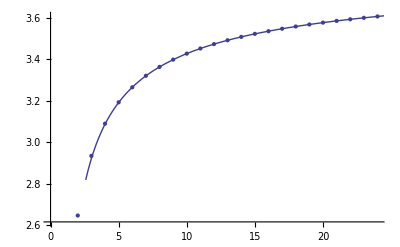

```mathematica
(*minimum variance*)
d=.480
nlm=NonlinearModelFit[norms⟦Range[8,24]⟧,a-b ((x-d )^(-c)),{a,b,c},x]
nlm["BestFitParameters"]
{f,g,h}=nlm[{"BestFit","FitResiduals","ParameterTable"}]
Total[g^2]/(Length[g]-1)
Show[ListPlot[norms],Plot[f,{x,0,37}]]
```

2.118

FittedModel[4.00001-1.22339/(-2.118+x)^0.36765]

{a→4.00001,b→1.22339,c→0.36765}

{4.00001-1.22339/(-2.118+x)^0.36765,{0.000499332,-0.000130328,-0.00050052,-0.00028628,-0.000281945,-0.0000260868,0.0000188674,0.000217707,0.000220655,0.000313324,0.000247841,0.000256826,0.00013451,0.0000688909,-0.000100224,-0.00022196,-0.000430607}, | Estimate | Standard Error | t-Statistic | P-Value
a | 4.00001 | 0.00750912 | 532.686 | 1.49034×10^-31
b | 1.22339 | 0.00240121 | 509.489 | 2.77958×10^-31
c | 0.36765 | 0.00553748 | 66.3931 | 6.68757×10^-19}

7.92836×10^-8

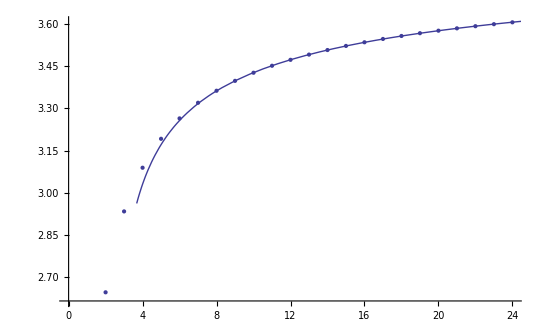

```mathematica
(*intersection with x axis for F to be amenable*)
d=2.118
nlm=NonlinearModelFit[norms⟦Range[8,24]⟧,a-b ((x-d )^(-c)),{a,b,c},x]
nlm["BestFitParameters"]
{f,g,h}=nlm[{"BestFit","FitResiduals","ParameterTable"}]
Total[g^2]/(Length[g]-1)
Show[ListPlot[norms],Plot[f,{x,0,37}]]
```